```mathematica
(*currWorkDir è,correntemente,la Directory di lavoro*)
currWorkDir=Directory[];
(*noteDir è la Directory di questo stesso Notebook*)
noteDir=NotebookDirectory[];
(*Lista dei Path noti al Kernel*)
$Path;
(*currWorkDir è già in $Path*)
(*noteDir non è ancora in $Path*)
Map[MemberQ[$Path#]&{currWorkDir, noteDir}];
```

```mathematica
(*Modo 1. Inseriamo noteDir in $Path*)
AppendTo[$Path, noteDir];
(*$Path=Append $Path,noteDir*)
```

```mathematica
(*Modo 2. Usiamo SetDirectory per far si' che noteDir diventi Directory corrente*)
```

```mathematica
SetDirectory[noteDir];
(*Ora la Directory corrente di lavoro è,appunto,noteDir*)
currWorkDir==SetDirectory[noteDir];
(*Prima di caricare il pacchetto quittare il kernel*)
```

```mathematica
(* Quit[]; *)
(*ClearAll"Global`*" non sara' sufficiente,perche' avremo Contesti differenti dal Global*)

SetDirectory[NotebookDirectory[]];
ff=FindFile["BadExample`"];
Get[ff]; (* Get vuole il path assoluto *)
```

```mathematica
(*NOTA.Dopo avere settato la Directory corretta,possiamo usare FindFile,che aiuta appunto a trovare un file*)(*ff=FindFile"BadExample`";
Getff*)
```

```mathematica
PowerSum[a,5]
```

a+a^2+a^3+a^4+a^5

```mathematica
PowerSum[x,5]
```

x+x^2+x^3+x^4+x^5

```mathematica
PowerSum[i,5]
```

3413

```mathematica
?PowerSum
```

```mathematica
(*Prima di caricare il pacchetto,quittare il kernel*)
```

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<BetterExample.m
```

```mathematica
PowerSum[a,5]
```

a+a^2+a^3+a^4+a^5

```mathematica
PowerSum[i,5]
```

i+i^2+i^3+i^4+i^5

```mathematica
(* Resta il problema che i simboli ausiliari i, n, x (usati in BetterExample) sono visibili anche nel contesto global *)
?Global`*
```

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<BestExample.m;
PowerSum[a,5]
PowerSum[i,5]
```

a+a^2+a^3+a^4+a^5

i+i^2+i^3+i^4+i^5

```mathematica
?Global`*
```

```mathematica
?Private`*
```

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MappaCartesiana.m
```

```mathematica
Context[CartesianMap]
```

MappaCartesiana`

```mathematica
$ContextPath
```

{MappaCartesiana`,System`,Global`}

```mathematica
Context[Curves]
```

Global`

```mathematica
?Curves
```

```mathematica
?CartesianMap
```

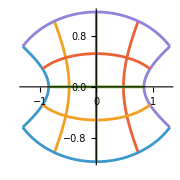

```mathematica
CartesianMap[Sin, {-1, 1, 0.5}, {-1, 1, 0.5}]
```

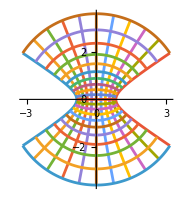

```mathematica
CartesianMap[Sin, {-1, 1, 0.2}, {-2, 2, 0.2}]
```

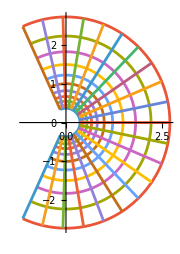

```mathematica
CartesianMap[ Exp, {-1, 1, 0.2}, {-2, 2, 0.2}]
```

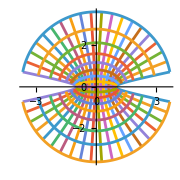

```mathematica
CartesianMap[ Cos, {0.2, Pi-0.2, (Pi-0.4)/19}, {-2, 2, 4/16}]
```

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MappaComplessa0.m
```

```mathematica
?PolarMap
```

```mathematica
?CartesianMap
```

```mathematica
?Picture
```

Missing[UnknownSymbol,Picture]

```mathematica
?Curves
```

Missing[UnknownSymbol,Curves]

```mathematica
$ContextPath
```

{MappaComplessa0`,System`,Global`}

```mathematica
{Context[PolarMap], Context[CartesianMap]}
```

{MappaComplessa0`,MappaComplessa0`}

```mathematica
{Context[Picture], Context[Curves]}
```

{Global`,Global`}

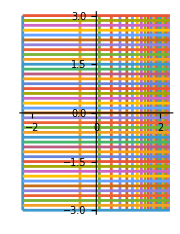

```mathematica
PolarMap[Log,{0.1,10,0.5},{-3,3,0.15}]
```

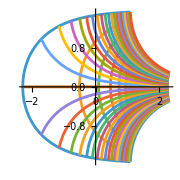

```mathematica
CartesianMap[Log,{0.1,10,0.5},{-3,3,0.15} ]
```

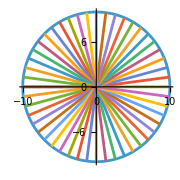

```mathematica
PolarMap[ 1 /Conjugate[#]&,{0.1,5.1,0.5},{-Pi,Pi,Pi/24}]
```

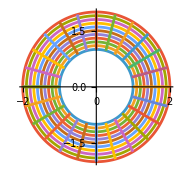

```mathematica
PolarMap[Identity,{1,2,0.1},{-Pi,Pi,Pi/12}]
```